```mathematica
rper:=0.7Rsun;
θper:=45*Pi/180;
Rper:=rper*Cos[θper];
zper:=rper*Sin[θper];

Mu=0.62;
γ=5/3;
ν=23;
kRoss=21.1; (* Rosseland opacity at 0.7 Rsun*)
χ=10^3*(16*T[Rper,zper]^3*sigmaSB*(γ-1)*Mu*mP)/(3*kRoss*ρ[Rper,zper]^2*kB)   (*this is what Goldreich and Schubert call χ*)
ξradiative = (γ-1)*χ   (*this is what Balbus and Schaan call ξrad*)
η=596;
```

2.13929×10^10

1.42619×10^10

```mathematica
NMaxIterations=70;
tEnd=3*10^7;
tref = Ω[Rper,zper]^-1
```

377013.

```mathematica
kR0:=-10^-4.5;
kϕ0=10^-7;
kz0:=10^-7;
kdotvA=Ω[Rper,zper];

kR[t_]:=kR0-Rper*kϕ0*t*ΩdR[Rper,zper];
kϕ[t_]:=kϕ0;
kz[t_]:=kz0-Rper*kϕ0*t*Ωdz[Rper,zper];

k[t_]:=(kR[t]^2+kϕ[t]^2+kz[t]^2)^(1/2);

vR0=-(kz0/kR0);
vϕ0=0;
vz0=1;

δρ0=0;
δCR0=0;
δCz0=0;
```

```mathematica
SolveTheSystem
```

{Null}

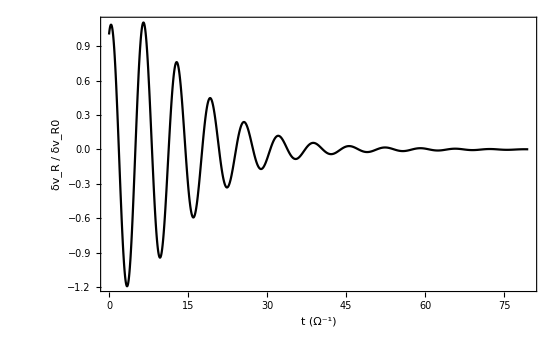

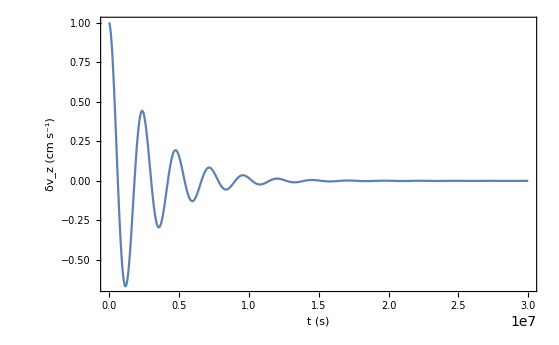

```mathematica
δvRPlot=Plot[δvRsol[t*tref]/δvRsol[0],{t,0,(tEnd/tref)},PlotRange->Full,Frame->True,FrameLabel->{"t (Ω^-1)","δv_R / δv_R0 ","k · v_A = Ω,  ξ_rad = 10^3 ξ_(rad⊙),  ν = ν_⊙,  η = η_⊙"},BaseStyle->{FontWeight->"Plain",FontSize->10},PlotStyle->Black,LabelStyle->Black]
Plot[δvzsol[t]/δvzsol[0],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δv_z (cm s^-1)"},BaseStyle->{FontWeight->"Plain",FontSize->14}]
Plot[δCRsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δC_R (gauss)"},BaseStyle->{FontWeight->"Plain",FontSize->14}];
Plot[δCzsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δC_z (gauss)"},BaseStyle->{FontWeight->"Plain",FontSize->14}];
Plot[δρsol[t],{t,0,tEnd},PlotRange->Full,Frame->True,FrameLabel->{"t (s)","δρ (g cm^-3)"},BaseStyle->{FontWeight->"Plain",FontSize->14}];
```

```mathematica
(*Export["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\Stability - Project 2\\GoldreichSchubert\\GS - Model A - Higher Thermal Diffusion With Magnetic Field\\picGS7.png",δvRPlot,ImageResolution->180];*)
```